```mathematica
f[a1_,x_,y_]:=x-x*y/(1+a1*x)-0.01*x*x;
```

```mathematica
g[a1_,d0_,x_,y_]:=-y+x*y/(1+a1*x)-d0*y*y;
```

```mathematica
funcr[a1_, d0_, x_] := -1-a1*x+x-d0*(1+2*a1*x+(a1^2)*x^2-0.01*x-0.02*a1*x^2-0.01*(a1^2)*x^3)
```

```mathematica
Solve[{funcr[0.9132,0.003,x]==0},x]
```

{{x→25.7877-14.2169 ⅈ},{x→25.7877+14.2169 ⅈ},{x→46.2345}}

```mathematica
equlibr[d0_]:=Solve[{funcr[0.9132,d0,x]==0},x]
```

```mathematica
Eq1X[d0_]:=x//.equlibr[d0][[1]]
```

```mathematica
Eq2X[d0_]:=x//.equlibr[d0][[2]]
```

```mathematica
Eq3X[d0_]:=x//.equlibr[d0][[3]]
```

```mathematica
EqY[d0_,x_]:= ((x/(1+0.9132*x))-1)/d0
```

```mathematica
Eq1X[0.003]
Eq2X[0.003]
Eq3X[0.003]
```

25.7877-14.2169 ⅈ

25.7877+14.2169 ⅈ

46.2345

```mathematica
EqY[0.003, Eq3X[0.003]]
```

23.2382

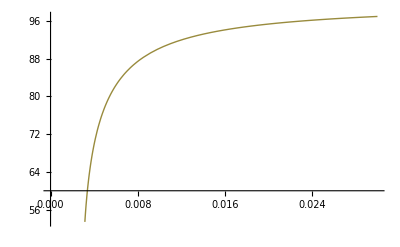

```mathematica
Plot[{Eq1X[d0],Eq2X[d0],Eq3X[d0]},{d0,0,0.03}]
```

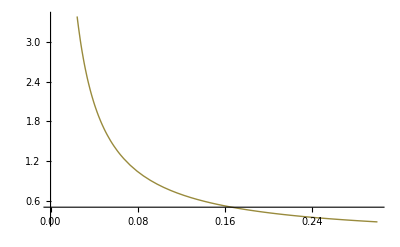

```mathematica
Plot[{EqY[d0,Eq1X[d0]], EqY[d0,Eq2X[d0]], EqY[d0,Eq3X[d0]]}, {d0, 0, 0.3}]
```

```mathematica
D[f[a1,x,y],x]
```

1-0.02 x+(a1 x y)/(1+a1 x)^2-y/(1+a1 x)

```mathematica
D[g[a1,d0,x,y],x]
```

-(a1 x y)/(1+a1 x)^2+y/(1+a1 x)

```mathematica
D[f[a1,x,y],y]
```

-x/(1+a1 x)

```mathematica
D[g[a1,d0,x,y],y]
```

-1+x/(1+a1 x)-2 d0 y

```mathematica
fx[a1_,x_,y_]:=D[f[a1,x,y],x];
```

```mathematica
fy[a1_,x_,y_]:=D[f[a1,x,y],y];
```

```mathematica
gx[a1_,d0_,x_,y_]:=D[g[a1,d0,x,y],x];
```

```mathematica
gy[a1_,d0_,x_,y_]:=D[g[a1,d0,x,y],y];
```

```mathematica
det[a1_,d0_,x_,y_,lam_]:=(1-0.02*x+(a1 x y)/(1+a1 x)^2-y/(1+a1 x)-lam)*(-1+x/(1+a1 x)-2 d0 y-lam)+x/(1+a1 x)*(-(a1 x y)/(1+a1 x)^2+y/(1+a1 x))
```

```mathematica
det[0.87,d0,x,y,lam]
```

(x (y/(1+0.87 x)-(0.87 x y)/(1+0.87 x)^2))/(1+0.87 x)+(-1-lam+x/(1+0.87 x)-2 d0 y) (1-lam-0.02 x-y/(1+0.87 x)+(0.87 x y)/(1+0.87 x)^2)

```mathematica
det1[d0_, x_, y_, lam_] :=(x (y/(1+0.9132 x)-(0.9132 x y)/(1+0.9132 x)^2))/(1+0.9132 x)+(-1-lam+x/(1+0.9132 x)-2 d0 y) (1-lam-0.02 x-y/(1+0.9132 x)+(0.9132 x y)/(1+0.9132 x)^2);
```

```mathematica
Solve[{det1[0.003, Eq3X[0.003], EqY[0.003, Eq3X[0.003]], lam]==0},lam]
```

{{lam→-0.00342245-0.0944041 ⅈ},{lam→-0.00342245+0.0944041 ⅈ}}

```mathematica
Test=Table[ lam/.Solve[{det1[d0, Eq2X[d0], EqY[d0, Eq2X[d0]], lam]==0},lam],{d0,0.01,1,0.0001}];
```

```mathematica
Test2=Table[ {d0,lam/.Solve[{det1[d0, Eq2X[d0], EqY[d0, Eq2X[d0]], lam]==0},lam][[1]]},{d0,0.0001,1,0.0001}];
```

```mathematica
Test3=Table[ {d0,lam/.Solve[{det1[d0, Eq2X[d0], EqY[d0, Eq2X[d0]], lam]==0},lam][[2]]},{d0,0.0001,1,0.0001}];
```

```mathematica
ListPlot[{Test2,Test3},PlotRange->{{0,0.2}, {-0.7, 0.7}}]
```

-Graphics-

```mathematica
TestM11=Table[ {d0,lam/.Solve[{det1[d0, Eq1X[d0], EqY[d0, Eq1X[d0]], lam]==0},lam][[1]]},{d0,0.01,1,0.0001}];
```

```mathematica
TestM12=Table[ {d0,lam/.Solve[{det1[d0, Eq1X[d0], EqY[d0, Eq1X[d0]], lam]==0},lam][[2]]},{d0,0.01,1,0.0001}];
```

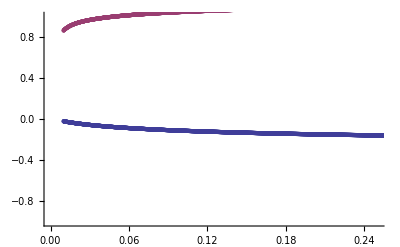

```mathematica
ListPlot[{Re[TestM11],Re[TestM12]},PlotRange->{{0,0.25},{-1, 1}}]
```

```mathematica
TestM31=Table[ {d0,lam/.Solve[{det1[d0, Eq3X[d0], EqY[d0, Eq3X[d0]], lam]==0},lam][[1]]},{d0,0.0001,0.3,0.0001}];
```

```mathematica
TestM32=Table[ {d0,lam/.Solve[{det1[d0, Eq3X[d0], EqY[d0, Eq3X[d0]], lam]==0},lam][[2]]},{d0,0.0001,0.3,0.0001}];
```

```mathematica
Export["C:\\Users\\Абрамова\\Desktop\\Новый курсач\\Курсач\\alpha=0,4\\Test2.txt", Test2, "List" ]
```

C:\Users\Абрамова\Desktop\Новый курсач\Курсач\alpha=0,4\Test2.txt

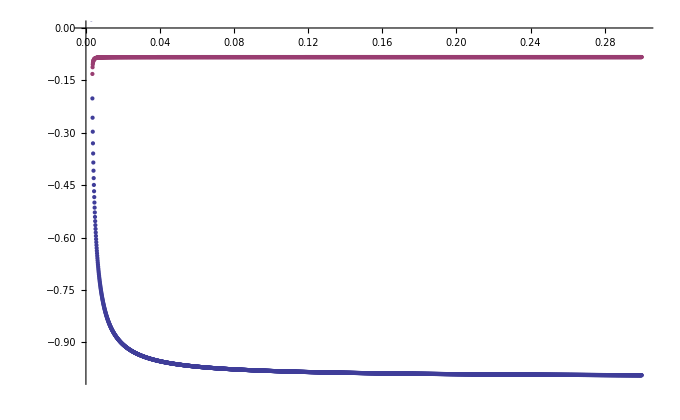

```mathematica
ListPlot[{TestM31,TestM32},PlotRange->{{0,0.3},{-1,0}}]
```

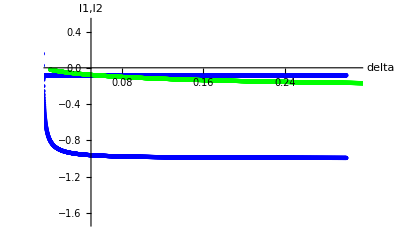

```mathematica
ListPlot[{Test2,Test3,TestM31,TestM32,Re[TestM11],Re[TestM12]},PlotRange->{{0.01,0.31},{-1.7,0.5}},PlotStyle->{Red,Red,Blue,Blue,Green,Green},AxesLabel->{Style["delta",Large],Style["l1,l2",Large]}]
```

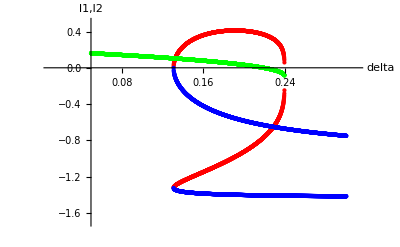

-Graphics-

```mathematica
S={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
W = {{w1, w2}, {w3, w4}}
```

{{w1,w2},{w3,w4}}

```mathematica
F = {{fx[a1, x, y], fy[a1, x, y]}, {gx[a1, d0, x, y], gy[a1, d0, x, y]}}
```

{{1-0.02 x+(a1 x y)/(1+a1 x)^2-y/(1+a1 x),-x/(1+a1 x)},{-(a1 x y)/(1+a1 x)^2+y/(1+a1 x),-1+x/(1+a1 x)-2 d0 y}}

```mathematica
R=F.W+W.Transpose[F]
```

{{-(w2 x)/(1+a1 x)-(w3 x)/(1+a1 x)+2 w1 (1-0.02 x+(a1 x y)/(1+a1 x)^2-y/(1+a1 x)),-(w4 x)/(1+a1 x)+w2 (-1+x/(1+a1 x)-2 d0 y)+w2 (1-0.02 x+(a1 x y)/(1+a1 x)^2-y/(1+a1 x))+w1 (-(a1 x y)/(1+a1 x)^2+y/(1+a1 x))},{-(w4 x)/(1+a1 x)+w3 (-1+x/(1+a1 x)-2 d0 y)+w3 (1-0.02 x+(a1 x y)/(1+a1 x)^2-y/(1+a1 x))+w1 (-(a1 x y)/(1+a1 x)^2+y/(1+a1 x)),2 w4 (-1+x/(1+a1 x)-2 d0 y)+w2 (-(a1 x y)/(1+a1 x)^2+y/(1+a1 x))+w3 (-(a1 x y)/(1+a1 x)^2+y/(1+a1 x))}}

```mathematica
MatrixForm[R]
```

(-(w2 x)/(1+0.4 x)-(w3 x)/(1+0.4 x)+2 w1 (1-0.02 x-y/(1+0.4 x)+(0.4 x y)/(1+0.4 x)^2) | -(w4 x)/(1+0.4 x)+w2 (-1+x/(1+0.4 x)-2 d0 y)+w1 (y/(1+0.4 x)-(0.4 x y)/(1+0.4 x)^2)+w2 (1-0.02 x-y/(1+0.4 x)+(0.4 x y)/(1+0.4 x)^2)
-(w4 x)/(1+0.4 x)+w3 (-1+x/(1+0.4 x)-2 d0 y)+w1 (y/(1+0.4 x)-(0.4 x y)/(1+0.4 x)^2)+w3 (1-0.02 x-y/(1+0.4 x)+(0.4 x y)/(1+0.4 x)^2) | 2 w4 (-1+x/(1+0.4 x)-2 d0 y)+w2 (y/(1+0.4 x)-(0.4 x y)/(1+0.4 x)^2)+w3 (y/(1+0.4 x)-(0.4 x y)/(1+0.4 x)^2))

```mathematica
R1[d0_,x_,y_]:=-(w2 x)/(1+a1 x)-(w3 x)/(1+a1 x)+2 w1 (1-0.02 x+(a1 x y)/(1+a1 x)^2-y/(1+a1 x));
```

```mathematica
R2[d0_,x_,y_]:=-(w4 x)/(1+a1 x)+w2 (-1+x/(1+a1 x)-2 d0 y)+w2 (1-0.02 x+(a1 x y)/(1+a1 x)^2-y/(1+a1 x))+w1 (-(a1 x y)/(1+a1 x)^2+y/(1+a1 x));
```

```mathematica
R3[d0_,x_,y_]:=-(w4 x)/(1+a1 x)+w3 (-1+x/(1+a1 x)-2 d0 y)+w3 (1-0.02 x+(a1 x y)/(1+a1 x)^2-y/(1+a1 x))+w1 (-(a1 x y)/(1+a1 x)^2+y/(1+a1 x));
```

```mathematica
R4[d0_,x_,y_]:=2 w4 (-1+x/(1+a1 x)-2 d0 y)+w2 (-(a1 x y)/(1+a1 x)^2+y/(1+a1 x))+w3 (-(a1 x y)/(1+a1 x)^2+y/(1+a1 x));
```

```mathematica
Clear[d]
```

```mathematica
d
```

d

```mathematica
solveW:= Solve[{{R1[d, Eq1X[d], EqY[d, Eq1X[d]]],R2[d, Eq1X[d], EqY[d, Eq1X[d]]]},{R3[d, Eq1X[d], EqY[d, Eq1X[d]]],R4[d, Eq1X[d], EqY[d, Eq1X[d]]]}}==-S,{w1,w2,w3,w4}]
```

```mathematica
solveW
```

{{w4→-0.5/(-1.+(32.6033+(«1»)/(«1»)-(«1»)/d)/(1.+0.4 («18»+(«1»)/(«1»)-(«1»)/d))-2. (-1.+(32.6033+((25.1803-«1») («1»))/(d («1»)^(1/3))-((15.8626+27.4748 ⅈ) («1»)^(1/3))/d)/(1.+0.9132 (32.6033+((«19»-«18» ⅈ) («1»-«1»))/(d («1»)^(1/3))-((15.8626+27.4748 ⅈ) «1»)/d))))+(«1»)/(«1»)+(0.5 (-(«1»)/(d «1»)+(«1»)/(d«1»«1»)) ((2. («1») ((1. («18»+(«1»)/(«1»)-(«1»)/d))/(1.+0.4 («1»))+0. («1»))-1. («1»))/(«1»)-(1. («1») («1»))/((2. («1») (0. («1»)+(«1»)/(«1»))+«1»)«1»«1»)))/(-1.+(«18»+«1»-«1»)/(1.«1»«4»«1»«1»)-2. (-1.+(32.6033+((«1»)«1»(«1»«1»)/(d («1»)^(«1»))-((«19»+«18» ⅈ) «1»)/d)/(1.+0.9132 (32.6033+(«1»)/(d «1»)-((«1») «1»)/d)))),«3»}}

```mathematica
a1=0.4
d=0.23
solveW
l1:= Eigenvalues[{{w1//.solveW[[1]],w2//.solveW[[1]]},{w3//.solveW[[1]],w4//.solveW[[1]]}}][[1]]
l2:= Eigenvalues[{{w1//.solveW[[1]],w2//.solveW[[1]]},{w3//.solveW[[1]],w4//.solveW[[1]]}}][[2]]
EigV := Eigenvectors[{{w1//.solveW[[1]],w2//.solveW[[1]]},{w3//.solveW[[1]],w4//.solveW[[1]]}}]
l1
l2
EigV
```

0.4

0.23

{{w1→-0.497532-0.452812 ⅈ,w2→-0.109741+0.294988 ⅈ,w3→-0.109741+0.294988 ⅈ,w4→0.387911-0.213913 ⅈ}}

-0.387322-0.395046 ⅈ

0.277702-0.271679 ⅈ

{{0.929962+0. ⅈ,0.0464292-0.364713 ⅈ},{-0.0464292+0.364713 ⅈ,0.929962+0. ⅈ}}

```mathematica
0.23
```

0.23